# Examples of sketches and forms

This Mathematica notebook is licensed under a .  It creates cells used in blog posts about sketches and forms appearing in Gyre&Gimble.
 
Charles Wells

## Line & arrow utilities

```mathematica
Subscript[ar,2]
```

ar_2

```mathematica
tp[p_,q_][x_]:=p[[2]]+((q[[2]]-p[[2]])/ (q[[1]]-p[[1]])) (x-p[[1]])
```

```mathematica
sint[m_,b_][x_]:=m x + b
```

```mathematica
ps[p_,m_][x_]:=p[[2]]+m (x-p[[1]])
```

```mathematica
slope[p_,q_]:=(q[[2]]-p[[2]])/(q[[1]]-p[[1]])
```

```mathematica
oslope[p_,q_]:=-(q[[1]]-p[[1]])/(q[[2]]-p[[2]])
```

```mathematica
loc[p_,q_,a_]:=a p+(1-a)q
```

```mathematica
midp[p_,q_]:=loc[p,q,1/2]
```

```mathematica
rlabelos[p_,m_,eps_]:=Module[
{om:=-1/(m)},
(x:=p[[1]]+Sqrt[eps^2(om^2+om^4)]/(1+om^2);y:=ps[{p[[1]],p[[2]]},-1/m][x];
{x,y})
]
```

```mathematica
llabelos[p_,m_,eps_]:=Module[
{om:=-1/(m)},
(x:=p[[1]]-Sqrt[eps^2(om^2+om^4)]/(1+om^2);y:=ps[{p[[1]],p[[2]]},-1/m][x];
{x,y})
]
```

## Basic tools

```mathematica
dnodes[diagramdata_]:=diagramdata[[1]];darrows[diagramdata_]:=diagramdata[[2]]
```

```mathematica
basediagram[diagramdata_,gap_,ahs_,thickness_]:={Arrowheads[ahs],Directive[Thickness[thickness]],Text[Style[#[[1]],Plain, Larger],#[[2]],Background->White]&/@dnodes[diagramdata],Arrow[{#[[2]],#[[3]]},Scaled[gap]]&/@darrows[diagramdata],Text[Style[#[[1]],Plain, Larger],(1/2)(#[[2]]+#[[3]]),Background->White]&/@darrows[diagramdata]}
```

```mathematica
cone[diagramdata_,vertexname_,vertexloc_,gap_,ahs_,key_,thickness_]:={Arrowheads[ahs],key,Text[vertexname,vertexloc],Directive[Thickness[thickness]],Background->Transparent,Arrow[{vertexloc,#},Scaled[gap]]&/@dnodes[diagramdata][[All,3]]}
```

```mathematica
limitplace[diagramdata_]:=Module[{nc=Length[dnodes[diagramdata]],xcoor=Plus @@dnodes[diagramdata][[All,3]][[All,1]],ycoor=Plus@@dnodes[diagramdata][[All,3]][[All,2]]},{xcoor/nc,ycoor/nc,.6nc}]
```

```mathematica
lp:=limitplace[obcpdiag]
```

```mathematica
darkgreen:=RGBColor[0,.6,0]
```

## Involutions

### Commutative diagram for involution

```mathematica
id[a_]:=Subscript["id",a]
```

```mathematica
id[c]
```

id_c

```mathematica
invcomdiag:={
{{C,{0,1}},{C,{1,1}},{C,{1,0}}
},
{{f,{0,1},{1,1}},{f,{1,1},{1,0}},{id[C],{0,1},{1,0}}
}
}
```

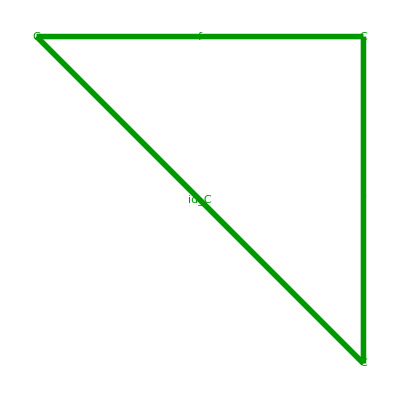

```mathematica
Show[Graphics[{Directive[darkgreen],basediagram[invcomdiag,.0003,.1,.01]},ImageSize->Tiny]]
```

```mathematica
mys[label_]:=Style[label,Plain,Larger,FontFamily->Arial]
```

```mathematica
llabelos[{.5,1},.1,.01]
```

{0.49005,1.0995}

```mathematica
llabelos[{0,0.5},1,.01]
```

{-0.00707107,0.507071}

```mathematica
midp[{0,1},{1,0}]
```

{1/2,1/2}

```mathematica
llabelos[midp[{0,1},{1,0}],-1,.1]
```

{0.429289,0.429289}

```mathematica
Show[
Graphics[
{Directive[darkgreen],
Arrowheads[.1],
Text[mys[C],{0,1}],
Text[mys[C],{1,1}],
Text[mys[C],{1,0}],
Arrow[{{0,1},{1,1}},.1],
Arrow[{{1,1},{1,0}},.1],
Arrow[{{0,1},{1,0}},.1],
Text[mys[f],llabelos[{.5,1},.1,.01]],
Text[mys[f],{1.1,.51}],
Text[mys[id[C]],llabelos[midp[{0,1},{1,0}],-1,.1]]
}
],
ImageSize->100
]
```

-Graphics-

### Sketch for involutions

```mathematica
Show[
Graphics[
{
Arrowheads[.1],
Text[mys[C],{0,1}],
Text[mys[C],{1,1}],
Text[mys[C],{1,0}],
Arrow[{{0,1},{1,1}},.1],
Arrow[{{1,1},{1,0}},.1],
Arrow[{{0,1},{1,0}},.1],
Text[mys[f],llabelos[{.5,1},.1,.01]],
Text[mys[f],{1.1,.51}],
Text[mys[id[C]],llabelos[midp[{0,1},{1,0}],-1,.1]]
}
],
ImageSize->100
]
```

-Graphics-

```mathematica
Show[
Graphics[
{
Arrowheads[.1],
Text[mys[C],{0,0}],
Arrow[BezierCurve[{{0,0},{-1,1},{1,1},{0,0}}],.2],
Text[mys[f],{0,.8},Background->White],
}
],
ImageSize->100
]
```

-Graphics-

### Limit cone in CS[FL,Cat] for formal endomorphisms

```mathematica
mannsty[node_,annot_]:=Style[node,Plain,Larger,FontFamily->Arial]^Style[annot,darkgreen,Plain,Larger,FontFamily->Arial]
```

```mathematica
mannsty[ob,C]
```

ob^C

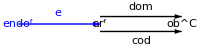

```mathematica
Show[
Graphics[
{
Arrowheads->Automatic,Blue,
Text[mannsty["endo" ,f],{0,0}],Black,
Text[mannsty[ar,f],{1,0}],
Text[mannsty[ob,C],{2,0}],Blue,
Arrow[{{0,0},{1,0}},{Scaled[.0007],Scaled[.0005]}],Black,
Arrow[{{1,.075},{2,.075}},Scaled[.0005]],
Arrow[{{1,-.075},{2,-.075}},Scaled[.0005]],Blue,
Text[mys[e],llabelos[{0.5,0},.1,.011]],Black,
Text[mys[dom],llabelos[{1.5,.15},.1,.002]],
Text[mys[cod],rlabelos[{1.5,-.15},.1,.002]]
}
],
ImageSize->200
]
```

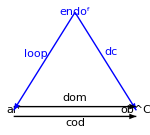

```mathematica
Show[
Graphics[
{
Arrowheads[.07],Blue,
Text[mannsty["endo" ,f],{.5,.8}],Black,
Text[mannsty[ar,f],{0,0}],
Text[mannsty[ob,C],{1,0}],Blue,
Arrow[{{.5,.8},{0,0}},{Scaled[.0003],Scaled[.0003]}],
Arrow[{{.5,.8},{1,0}},{Scaled[.0003],Scaled[.0003]}],Black,
Arrow[{{0,.03},{1,.03}},Scaled[.0005]],
Arrow[{{0,-.05},{1,-.05}},Scaled[.0005]],Blue,
Text[mys[loop],rlabelos[{0.17,.56},.1,.01],Background->White],Text[mys[dc],llabelos[{0.8,.38},.1,.01],Background->White],Black,
Text[mys[dom],llabelos[{.5,.1},.1,.0001]],
Text[mys[cod],rlabelos[{.5,-.1},.1,.0001]]
}
],
ImageSize->150
]
```

### Limit cone in CS[FL,Cat] that defines composable pairs

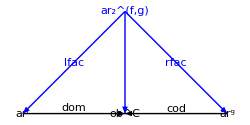

```mathematica
Show[
Graphics[
{
Arrowheads->Automatic,Blue,
Text[mannsty[Subscript[ar,2] ,"(f,g)"],{1,1}],Black,
Text[mannsty[ar,f],{0,0}],
Text[mannsty[ar,g],{2,0}],
Text[mannsty[ob,C],{1,0}],Blue,
Arrow[{{1,1},{0,0}},{Scaled[.0004],Scaled[.0003]}],
Arrow[{{1,1},{1,0}},{Scaled[.0003],Scaled[.0003]}],
Arrow[{{1,1},{2,0}},{Scaled[.0003],Scaled[.0003]}],Black,
Arrow[{{0,0},{1,0}},Scaled[.0005]],
Arrow[{{2,0},{1,0}},Scaled[.0005]],Blue,
Text[mys[lfac],{0.5,.5},Background->White],Text[mys[rfac],{1.5,.5},Background->White],Black,
Text[mys[dom],llabelos[{.5,0.05},.1,.0001]],
Text[mys[cod],rlabelos[{1.5,0.05},.1,.0001]]
}
],
ImageSize->250
]
```

### Sawhorse in CS[FL, Cat] that defines inclusion of endo into composable pairs]

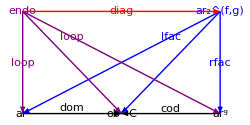

```mathematica
Show[
Graphics[
{
Arrowheads[.04],Blue,
Text[mannsty[Subscript[ar,2] ,"(f,g)"],{2,1}],Black,
Text[mannsty[ar,f],{0,0}],
Text[mannsty[ar,g],{2,0}],
Text[mannsty[ob,C],{1,0}],Blue,
Arrow[{{2,1},{0,0}},{Scaled[.0005],Scaled[.0004]}],
Arrow[{{2,1},{1,0}},{Scaled[.0005],Scaled[.0004]}],
Arrow[{{2,1},{2,0}},{Scaled[.0003],Scaled[.0003]}],Purple,
Arrow[{{0,1},{0,0}},{Scaled[.0003],Scaled[.0004]}],
Arrow[{{0,1},{1,0}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{0,1},{2,0}},{Scaled[.0005],Scaled[.0003]}],
Text[mys[endo],{0,1}],
Text[mys[loop],{0,.5},Background->White],
Text[mys[loop],{.5,.75},Background->White],
Red,
Arrow[{{0,1},{2,1}},{Scaled[.0008],Scaled[.0007]}],
Text[mys[diag],{1,1},Background->White],
Black,
Arrow[{{0,0},{1,0}},Scaled[.0005]],
Arrow[{{2,0},{1,0}},Scaled[.0005]],Blue,
Text[mys[lfac],{1.5,.75},Background->White],Text[mys[rfac],{2,.5},Background->White],Black,
Text[mys[dom],llabelos[{.5,0.05},.1,.0001]],
Text[mys[cod],rlabelos[{1.5,0.05},.1,.0001]]
}
],
ImageSize->250
]
```

### Limit cone in CS[FL,Cat] for formal involution

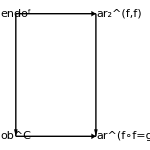

```mathematica
Show[
Graphics[
{
Arrowheads[.07],Black,
Text[mannsty[endo,f],{0,1}],Black,
Text[mannsty[Subscript[ar,2],"(f,f)"],{1,1},{-.7,0}],
Text[mannsty[ar,"f∘f=g"],{1,0},{-.7,0}],
Text[mannsty[ob,C],{0,0}],Arrow[{{0,1},{1,1}},{Scaled[.0006],Scaled[.0004]}],
Arrow[{{0,1},{0,0}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{1,1},{1,0}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{0,0},{1,0}},{Scaled[.0006],Scaled[.0004]}]
}
],ImageSize->150
]
```

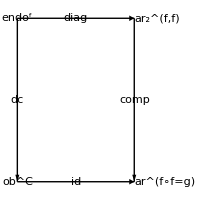

```mathematica
Show[
Graphics[
{
Arrowheads[.07],Black,
Text[mannsty[endo,f],{0,1}],Black,
Text[mannsty[Subscript[ar,2],"(f,f)"],{1,1},{-.7,0}],
Text[mannsty[ar,"f∘f=g"],{1,0},{-.7,0}],
Text[mannsty[ob,C],{0,0}],Arrow[{{0,1},{1,1}},{Scaled[.0006],Scaled[.0004]}],
Arrow[{{0,1},{0,0}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{1,1},{1,0}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{0,0},{1,0}},{Scaled[.0006],Scaled[.0004]}],
Text[mys[comp],{1,.5},Background->White],Text[mys[dc],{0,.5},Background->White],Text[mys[diag],{.5,1},Background->White],Text[mys[id],{.5,0},Background->White]
}
],ImageSize->200
]
```

```mathematica
Show[
Graphics3D[
{
Arrowheads[.035],Black,
Text[mannsty[endo,f],{0,1,0},Background->White],
Text[mannsty[Subscript[ar,2],"(f,f)"],{1,1,0},{-.7,0},Background->White],
Text[mannsty[ar,"f∘f=g"],{1,0,0},{-.7,0},Background->White],
Text[mannsty[ob,C],{0,0,0},Background->White],Arrow[{{{0,1,0},{1,1,0}}},{Scaled[.0004],Scaled[.0004]}],
Arrow[{{{0,1,0},{0,0,0}}},{Scaled[.0002],Scaled[.0004]}],
Arrow[{{{1,1,0},{1,0,0}}},{Scaled[.0002],Scaled[.0004]}],
Arrow[{{{0,0,0},{1,0,0}}},{Scaled[.0004],Scaled[.0004]}],
Text[mys[comp],{1,.5,0},Background->White],Text[mys[dc],{0,.5,0},Background->White],Text[mys[diag],{.5,1,0},Background->White],Text[mys[id],{.5,0,0},Background->White],Blue,
Arrow[{{{0.5,0.5,1},{1,1,0}}},{Scaled[.0002],Scaled[.0004]}],Arrow[{{{0.5,0.5,1},{0,0,0}}},{Scaled[.0002],Scaled[.0004]}],Arrow[{{{0.5,0.5,1},{1,0,0}}},{Scaled[.0002],Scaled[.0004]}],Arrow[{{{0.5,0.5,1},{0,1,0}}},{Scaled[.0002],Scaled[.0004]}],Text[mys[inv],{.5,.5,1},Background->White]
},Boxed->False,PlotRangePadding->.1,PlotRange->All
],ImageSize->300
]
```

-Graphics3D-

## Magmas

### Cone for formal object of pairs of objects

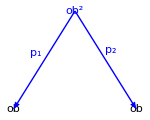

```mathematica
Show[
Graphics[
{
Arrowheads[.07],Blue,
Text[mys[Superscript[ob,2]],{.5,.8}],Black,
Text[mys[ob],{0,0}],
Text[mys[ob],{1,0}],Blue,
Arrow[{{.5,.8},{0,0}},{Scaled[.0003],Scaled[.0003]}],
Arrow[{{.5,.8},{1,0}},{Scaled[.0003],Scaled[.0003]}],Blue,
Text[mys[Subscript[p,1]],rlabelos[{0.17,.56},.1,.01],Background->White],Text[mys[Subscript[p,2]],llabelos[{0.8,.38},.1,.01],Background->White]
}
],
ImageSize->150
]
```

### Cone defining formal set of product cones

### Cone defining formal magma

## Example from Showing categorical diagrams in 3 D

```mathematica
(*diagramdata: is a list of objects (dnodes) and a list of arrows (darrows).*)
obcpdiag:={{{ar,1,{1.5,2,0}},{ar,2,{3,2,0}},{ob,3,{0,0,0}},{ob,4,{2,0,0}},{ob,5,{4,0,0}}},{{dom,6,{1.5,2,0},{0,0,0}},{cod,7,{1.5,2,0},{2,0,0}},{dom ,8,{3,2,0},{2,0,0}},{cod,9,{3,2,0},{4,0,0}}}}
```

```mathematica
Show[Graphics3D[basediagram3D[obcpdiag,.0007,.02,.002]]]
```

```mathematica
Manipulate[Show[Graphics3D[{basediagram3D[obcpdiag,.0007,.02,.002],cone[obcpdiag,cp,lp+{1.6,1,0},.0007,.02,c1,.002],Text[Style[ar,Plain,c2],lp-{.75,.75,0},Background->White],
Text[Style[rfac,Plain,c1],(1/2)(lp+{1.6,1,0}+{1.5,2,0}),Background->White],Text[Style[lfac,Plain,c1],(1/2)(lp+{1.6,1,0}+{3,2,0}),Background->White],Text[Style[dom,Plain,c2],(1/2)(lp-{.75,.75,0}+{0,0,0}),Background->White],Text[Style[cod,Plain,c2],(1/2)(1.05(lp-{.75,.75,0})+.95{4,0,0}),Background->White],Text[Style[comp,Plain,c3],(1/2)(2 lp+{1.6,1,0}-{.75,.75,0}),Background->White],
Directive[c1,Thickness[c4]],Arrow[{{lp+{1.6,1,0},{0,0,0}}},Scaled[.0007]],Arrow[{{lp+{1.6,1,0},{4,0,0}}},Scaled[.0007]],Directive[c2,Thickness[c4]],Arrow[{{lp-{.75,.75,0},{0,0,0}}},Scaled[.0007]],Arrow[{{lp-{.75,.75,0},{4,0,0}}},Scaled[.0007]],
Directive[c3],Arrow[{{lp+{1.6,1,0},lp-{.75,.75,0}}},Scaled[.0007]]},
ImageSize->400,BaseStyle->{FontFamily->"Arial",FontSize->12},Boxed->False,ImagePadding->40,ViewPoint->{-9,30,-20}]],{c1,{Transparent,Blue},ControlType->Checkbox},{c2,{Transparent,darkgreen},ControlType->Checkbox},{c3,{Transparent,Red},ControlType->Checkbox},{c4,{.002,.004},ControlType->Checkbox},ControlPlacement -> Left,SaveDefinitions->True]
```